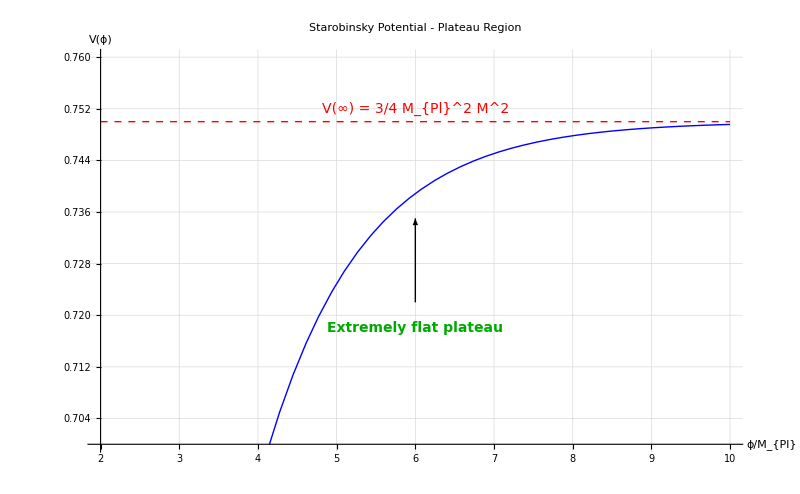

```mathematica
MPl=1;
M=1;
V[phi_]:=(3 MPl^2 M^2)/4 (1-Exp[-Sqrt[2/3] phi/MPl])^2
Vinf=3/4;
Plot[V[phi],{phi,2,10},PlotStyle->{Thick,Blue},AxesLabel->{"ϕ/M_{Pl}","V(ϕ)"},PlotLabel->Style["Starobinsky Potential - Plateau Region",16],GridLines->Automatic,ImageSize->800,PlotRange->{0.7,0.76},Epilog->{{Dashed,Red,Thick,Line[{{2,Vinf},{10,Vinf}}]},Text[Style["V(∞) = 3/4 M_{Pl}^2 M^2",Red,14],{6,0.752}],Text[Style["Extremely flat plateau",Darker[Green],14,Bold],{6,0.718}],Arrow[{{6,0.722},{6,0.735}}]}]
```